```mathematica
Clear[h,n,t]
$Assumptions=h∈Reals&&h≥0&&t∈Reals&&t≥0&&n∈Reals&&n>0&&τ∈Reals;
```

```mathematica
(*Sz spin operator (s=1)*)
Sz = DiagonalMatrix[{1, 0, -1}];
```

```mathematica
(*Sx spin operator*)
Sx = {{0,1/Sqrt[2],0},{1/Sqrt[2],0,1/Sqrt[2]},{0,1/Sqrt[2],0}};
```

```mathematica
(*Hamiltonian - Considering that the quench happens at t=0*)
H[h_,t_]:= -(1-h*(Tanh[100*t]+1)/2)*Sz-(h*(Tanh[100*t]+1)/2/n)*Sx.Sx;
```

```mathematica
(*Eigenvalues and eigenvectors of the initial hamiltonian*)
Vinit =FullSimplify[ Eigenvectors[H[0,-1]]]; 
Eginit = FullSimplify[Eigenvalues[H[0,-1]]];
```

```mathematica
(*Time evolution opeartor*)
U[t_] := FullSimplify[MatrixExp[-I*t*(-(1-h)*Sz - (h/n)*Sx.Sx)]]

(*Initial density matrix Subscript[ρ, 0] = |3><3|*)
rho0 =ArrayReshape[Vinit[[3]],{3,1}].ArrayReshape[Vinit[[3]],{1,3}]
```

{{0,0,0},{0,1,0},{0,0,0}}

```mathematica
(*ρ(t) = Subscript[Uρ, 0] U^\dag*)
rhot=FullSimplify[U[t].rho0.ConjugateTranspose[U[t]]];
```

```mathematica
(*Using the notation of Lucas's paper:
H(t) = Subscript[u, t] Subscript[h, t] Subscript[u, t]'*)
u = FullSimplify[Transpose[Assuming[Element[h|t|n,Reals],Eigenvectors[H[h,t]]]]];
```

$Aborted

```mathematica
Q = Integrate[FullSimplify[Tr[FullSimplify[rhot.D[u,t].DiagonalMatrix[Eigenvalues[H[h,t]]].Inverse[u]]+FullSimplify[rhot.u.DiagonalMatrix[Eigenvalues[H[h,t]]].D[Inverse[u],t]]]],{t,0,τ}]
```

0

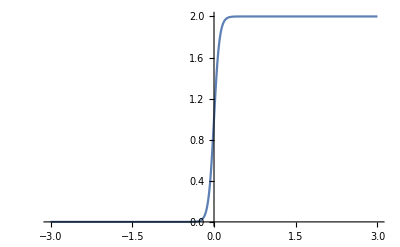

```mathematica
Plot[Tanh[10*x]+1,{x,-3,3}]
```